# Diffraction Cross Section

```mathematica
(* the d.c.s. is proportional to the sqaure of f[k,k'], which is the amplitude of scattered spherical wave *)
```

```mathematica
(* The Born Approximation *)
```

```mathematica
(* From J.J.Sakurai Book P.386 *)
f[θ_,V_,q_]:= (-2 m)/(ℏ^2 2 q)∫_0^∞ r V Sin[r q]ⅆr
```

```mathematica
(* From Introduction of Nuclear and Particle Physics, P.20 *)
F[θ_,ρ_]:=∫ρ Exp[ⅈ 2  Sin[θ/2] p.r]ⅆV
(* which is Fourier Transform in 3D *)
p.r = p r Cos[α]
```

## For Yukawa potential

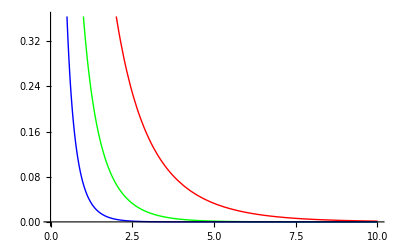

```mathematica
V[μ_,r_]:=ⅇ^(-μ r)/(μ r)
Plot[{V[0.5,r],V[1,r],V[2,r]},{r,0,10},PlotStyle->{Red, Green ,Blue}]
```

```mathematica
dscY[θ_,α_]:=1/((1-Cos[θ])+α)^2
Manipulate[Plot[dscY[θ,α],{θ,0,π},PlotRange->{0,All}],{α,0,10}]
```

## Coulomb Potential

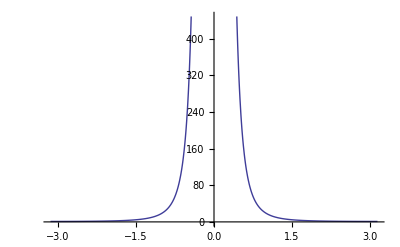

```mathematica
dscC[θ_]:=1/Sin[θ/2]^4
Plot[dscC[θ],{θ,-π,π}]
```

## Arbitary

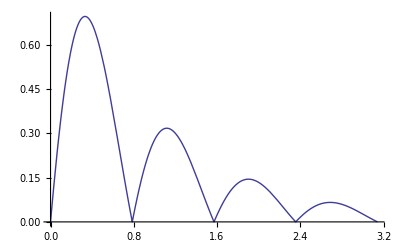

```mathematica
Plot[Exp[-θ] Abs[Sin[4θ]],{θ,0,π}]
```

```mathematica
f[θ,Exp[-r] Abs[Sin[4r]],q]
```

$Aborted

## Fourier Transform 3-D

```mathematica
F[p_,ρ_]:=∫_0^(2π) ∫_0^π ∫_0^∞ ρ Exp[ⅈ p r Cos[α]] r^2 Sin[α]ⅆr ⅆα ⅆ β
```

```mathematica
F[k,1/r]
```

(4 π)/k^2

```mathematica
F[k,1/r^3]
```

Integrate::idiv: Integral of ⅇ^ⅈ k r Cos[α]/r does not converge on {0, ∞}.

∫_0^(2 π) ∫_0^π ∫_0^∞ (ⅇ^(ⅈ k r Cos[α]) Sin[α])/r ⅆrⅆαⅆβ

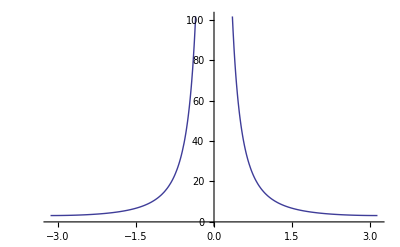

```mathematica
Plot[π Csc[θ/2]^2,{θ,-π,π}]
```

```mathematica
(* use build -in function *)
FourierTransform[1/(x^2+y^2),{x,y},{u,v}]
```

1/2 (-HeavisideTheta[-u] (2 EulerGamma+Log[-u-ⅈ v]+Log[-u+ⅈ v])-HeavisideTheta[u] (2 EulerGamma+Log[u-ⅈ v]+Log[u+ⅈ v]))

```mathematica
FourierTransform[Exp[-x^2],x,u]
```

(ⅇ^(-u^2/4))/(√2)

```mathematica
1/(√(2π))∫_(-∞)^∞ Exp[-x^2]Exp[ⅈ u x]ⅆx
```

(ⅇ^(-u^2/4))/(√2)

```mathematica
FourierTransform[FourierTransform[1/(√(x^2+y^2)),x,u],y,v]
```

1/(√(u^2+v^2))

```mathematica
∫_0^(2π) ∫_0^∞ Exp[ⅈ k r Cos[θ]Cos[α]+ⅈ k r Sin[θ]Sin[α]] ⅆr ⅆ θ
```

1/k ⅈ If[α∉Reals||2 Re[α]≥5 π||π+2 Re[α]≤0,-Log[-Cos[α/2]-Sin[α/2]]-Log[Cos[α/2]-Sin[α/2]]+Log[-Cos[α/2]+Sin[α/2]]+Log[Cos[α/2]+Sin[α/2]],Integrate[Sec[θ-α],{θ,0,2 π},Assumptions→!(α∉Reals||2 Re[α]≥5 π||π+2 Re[α]≤0)]]

```mathematica
∫_0^(2π) Exp[ⅈ k r Cos[θ]] ⅆ θ
```

If[k r∈Reals,2 π BesselJ[0,k r],Integrate[ⅇ^(ⅈ k r Cos[θ]),{θ,0,2 π},Assumptions→k r∉Reals]]

```mathematica
Integrate[2 π BesselJ[0,k r],{r,0,∞}]
```

$Aborted

```mathematica
FourierTransform[1/r,r,k,FourierParameters->{0, Cos[θ]}]
```

ⅈ √(π/2) √Abs[Cos[θ]] Sign[k Cos[θ]]

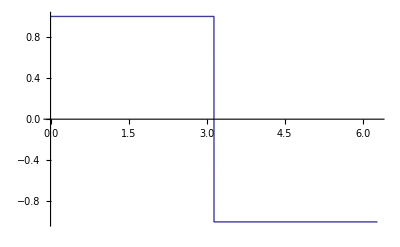

```mathematica
Plot[Sign[Sin[θ]],{θ,0,2 π}]
```

```mathematica
FourierTransform[Sign[Sin[x]],x,k]
```

$Aborted

```mathematica
Integrate[%,{θ,0,2π}]
```

∫_0^(2 π) ⅈ √(π/2) √Abs[Cos[θ]] Sign[k Cos[θ]]ⅆθ